# HW 5 - ASTR510

## Daniel George

## Q2)

## a)

### Function to move a photon one step forward

```mathematica
move[dx_,τ_]:=Function[v,{v[[1]]+dx#,#}&@If[RandomReal[]<τ,{Cos[#],Sin[#]}&@RandomReal[{0,2Pi}],v[[2]]]];
```

### Function to computing the final angles of n photons

```mathematica
data[n_]:=data[n]=Mod[Pi/2+#,2Pi]&[ArcTan@@@ParallelTable[NestWhile[move[.01,.01],{{0,-1},RandomPoint@Circle[]},Total[#[[1]]^2]≤1&][[2]],n]];
```

## b)

### Plotting intensity as a fraction of brightness vs angle for 10^6 photons

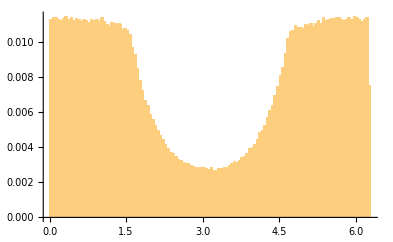

```mathematica
Histogram[data[10^6],100,"Probability"]
```

## c)

### Computing histograms for number of photons = {5*10^5, 10^5, 5*10^4, 10^4, 5*10^3,10^3}

```mathematica
hdata[n_]:=hdata[n]=HistogramList[data[n],100,"Probability"][[2]]
```

### Finding maximum relative error with respect to histogram for 10^6 photons

```mathematica
err=Max[1. Abs[hdata[#]-hdata[10^6]]/hdata[10^6]]&/@{10^6,5*10^5,10^5,5*10^4,10^4,5*10^3,10^3};
```

### Log-log plot of maximum relative error vs number of photons

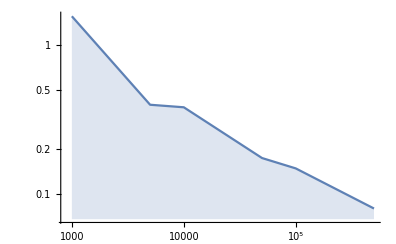

```mathematica
ListLogLogPlot[Transpose@{{10^6,5*10^5,10^5,5*10^4,10^4,5*10^3,10^3},err},Joined->True,Filling->Bottom]
```

### Finding slope of best fit line to the log-log plot

```mathematica
f[x_]=Fit[Log@Transpose@{{5*10^5,10^5,5*10^4,10^4,5*10^3,10^3},err[[2;;]]},{1,x},x]
```

3.2407-0.450743 x

The slope of the line is approximately -0.5. Therefore the maximum relative error in the intensity decreases as N^-0.5.